```mathematica
WorkOnGraph4[g_Graph,vertices_List]:=Block[{split,left, right,left2,right2,middle2,middle,sols,lefta,middlea,righta,middleC, table},
split= ConnectedComponents[VertexDelete[g,vertices]];
left=VertexDelete[g,split[[1]]];
right=VertexDelete[g,split[[2]]];
middle=CycleGr[vertices];
left2=MakeComplete[left,vertices];
right2=MakeComplete[right,vertices];
middle2=MakeComplete[middle,vertices];
sols=Map[SymbolToSets,FindFullFormula[middle]]//Reverse;
table=Table[
middlea=ApplyToGraph[middle2,sol];
lefta=Graph[ApplyToGraph[left2,sol],GraphHighlight->EdgeList[middlea],GraphHighlightStyle->"Thick",ImageSize->200];
righta=Graph[ApplyToGraph[right2,sol],GraphHighlight->EdgeList[middlea],GraphHighlightStyle->"Thick",ImageSize->200];
middleC=ChromaticPolynomial[middlea,x];
{Factor[Simplify[ChromaticPolynomial[lefta,x]*ChromaticPolynomial[righta,x]/middleC]]},
{sol,sols}
];
TableForm[
AppendTo[table,Expand[Total[table]]]
]
]
```

```mathematica
With[{k=10000},
Block[{g=ReadGrof[k],vertices, adj},
vertices=Select[VertexList[g],VertexDegree[g,#]==5&];
Table[
adj=AdjacencyList[g,v];
{Style[k,If[OddQ[k],Blue,Purple]],v}->Labeled[Framed[WorkOnGraph4[g,adj]],adj]
,{v,vertices}
]
]
]
```

{{10000,9}→(-3+x)^5 (-2+x)^2 (-1+x) x (-32+29 x-9 x^2+x^3)
(-3+x)^7 (-2+x)^3 (-1+x) x
(-4+x)^2 (-3+x)^4 (-2+x)^2 (-1+x) x (-32+29 x-9 x^2+x^3)
(-3+x)^8 (-2+x)^2 (-1+x) x
(-3+x)^8 (-2+x)^2 (-1+x) x
(-4+x)^2 (-3+x)^5 (-2+x) (-1+x) x (-32+29 x-9 x^2+x^3)
(-3+x)^8 (-2+x)^2 (-1+x) x
(-4+x)^2 (-3+x)^5 (-2+x) (-1+x) x (-32+29 x-9 x^2+x^3)
(-4+x)^2 (-3+x)^7 (-2+x)^2 (-1+x) x
(-4+x)^2 (-3+x)^7 (-2+x)^2 (-1+x) x
(-5+x)^2 (-4+x) (-3+x)^5 (-2+x) (-1+x) x (-32+29 x-9 x^2+x^3)
-739044 x+3524256 x^2-7601499 x^3+9876522 x^4-8663128 x^5+5437056 x^6-2519771 x^7+875492 x^8-228610 x^9+44405 x^10-6248 x^11+604 x^12-36 x^13+x^14{2,3,5,12,6},{10000,6}→(-3+x)^8 (-2+x)^2 (-1+x) x
(-3+x)^8 (-2+x)^2 (-1+x) x
(-4+x)^3 (-3+x)^6 (-2+x)^2 (-1+x) x
(-3+x)^8 (-2+x)^2 (-1+x) x
(-3+x)^9 (-2+x) (-1+x) x
(-4+x)^2 (-3+x)^8 (-2+x) (-1+x) x
(-3+x)^9 (-2+x) (-1+x) x
(-4+x)^2 (-3+x)^8 (-2+x) (-1+x) x
(-4+x)^2 (-3+x)^8 (-2+x) (-1+x) x
(-4+x)^3 (-3+x)^7 (-2+x) (-1+x) x
(-5+x)^2 (-4+x)^2 (-3+x)^7 (-2+x) (-1+x) x
-810648 x+3894318 x^2-8456643 x^3+11048265 x^4-9726480 x^5+6112134 x^6-2827949 x^7+977647 x^8-253063 x^9+48535 x^10-6716 x^11+636 x^12-37 x^13+x^14{3,5,9,13,10},{10000,8}→(-3+x)^8 (-2+x) (-1+x) x
(-3+x)^7 (-2+x)^2 (-1+x) x
(-4+x) (-3+x)^8 (-2+x) (-1+x) x
(-3+x)^8 (-2+x) (-1+x) x
(-3+x)^8 (-2+x) (-1+x) x
(-4+x)^2 (-3+x)^7 (-2+x) (-1+x) x
(-3+x)^8 (-2+x) (-1+x) x
(-4+x)^2 (-3+x)^7 (-2+x) (-1+x) x
(-4+x) (-3+x)^8 (-2+x) (-1+x) x
(-4+x) (-3+x)^8 (-2+x) (-1+x) x
(-5+x) (-4+x)^2 (-3+x)^7 (-2+x) (-1+x) x
113724 x-540918 x^2+1157652 x^3-1481490 x^4+1267299 x^5-765558 x^6+335622 x^7-107782 x^8+25200 x^9-4188 x^10+470 x^11-32 x^12+x^13{3,5,13,4,10},{10000,13}→(-3+x)^8 (-2+x) (-1+x) x
(-3+x)^7 (-2+x)^2 (-1+x) x
(-4+x) (-3+x)^8 (-2+x) (-1+x) x
(-3+x)^8 (-2+x) (-1+x) x
(-3+x)^8 (-2+x) (-1+x) x
(-4+x)^2 (-3+x)^7 (-2+x) (-1+x) x
(-3+x)^8 (-2+x) (-1+x) x
(-4+x)^2 (-3+x)^7 (-2+x) (-1+x) x
(-4+x) (-3+x)^8 (-2+x) (-1+x) x
(-4+x) (-3+x)^8 (-2+x) (-1+x) x
(-5+x) (-4+x)^2 (-3+x)^7 (-2+x) (-1+x) x
113724 x-540918 x^2+1157652 x^3-1481490 x^4+1267299 x^5-765558 x^6+335622 x^7-107782 x^8+25200 x^9-4188 x^10+470 x^11-32 x^12+x^13{3,6,8,4,10},{10000,10}→(-3+x)^7 (-2+x)^2 (-1+x) x
(-3+x)^8 (-2+x) (-1+x) x
(-4+x) (-3+x)^8 (-2+x) (-1+x) x
(-3+x)^8 (-2+x) (-1+x) x
(-3+x)^8 (-2+x) (-1+x) x
(-4+x) (-3+x)^8 (-2+x) (-1+x) x
(-3+x)^8 (-2+x) (-1+x) x
(-4+x) (-3+x)^8 (-2+x) (-1+x) x
(-4+x)^2 (-3+x)^7 (-2+x) (-1+x) x
(-4+x)^2 (-3+x)^7 (-2+x) (-1+x) x
(-5+x) (-4+x)^2 (-3+x)^7 (-2+x) (-1+x) x
113724 x-540918 x^2+1157652 x^3-1481490 x^4+1267299 x^5-765558 x^6+335622 x^7-107782 x^8+25200 x^9-4188 x^10+470 x^11-32 x^12+x^13{5,6,8,13,4}}

```mathematica
(-3+x)^4(-3+x)^2 (-32+29 x-9 x^2+x^3)*ChromaticPolynomial[CompleteGraph[3],x]+(-5+x) (-3+x)^3*(-5+x) (-3+x) (-32+29 x-9 x^2+x^3)*ChromaticPolynomial[CompleteGraph[4],x]//Expand
```

342144 x-1533492 x^2+3070332 x^3-3652029 x^4+2885964 x^5-1601137 x^6+641047 x^7-186987 x^8+39503 x^9-5903 x^10+593 x^11-36 x^12+x^13

```mathematica
ChromaticPolynomial[ReadGrof[10000],x]//Factor
```

(-3+x)^7 (-2+x) (-1+x) x (-32+29 x-9 x^2+x^3)

```mathematica
WorkOnGraph[g_Graph,vertices_List]:=Block[{split,left, right,left2,right2,middle2,middle,sols,lefta,middlea,righta},
split= ConnectedComponents[VertexDelete[g,vertices]];
left=VertexDelete[g,split[[1]]];
right=VertexDelete[g,split[[2]]];
middle=VertexDelete[g,Select[DeleteDuplicates[Join[VertexList[left],VertexList[right]]],!MemberQ[vertices,#]&]];
left2=MakeComplete[left,vertices];
right2=MakeComplete[right,vertices];
middle2=MakeComplete[middle,vertices];
sols=Map[SymbolToSets,FindFullFormula[middle]]//Reverse;
TableForm[
Table[
middlea=ApplyToGraph[middle2,sol];
lefta=Graph[ApplyToGraph[left2,sol],GraphHighlight->EdgeList[middlea],GraphHighlightStyle->"Thick",ImageSize->200];
righta=Graph[ApplyToGraph[right2,sol],GraphHighlight->EdgeList[middlea],GraphHighlightStyle->"Thick",ImageSize->200];
{SolToSymbol[sol,vertices]/.RepGraph["C"],GraphWithChrom[lefta],GraphWithChrom[righta],GraphWithChrom[middlea],Graph[middle,VertexLabels->"Name"]},
{sol,sols}
]
]
]
```

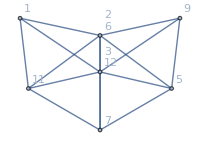
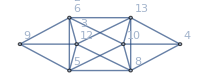
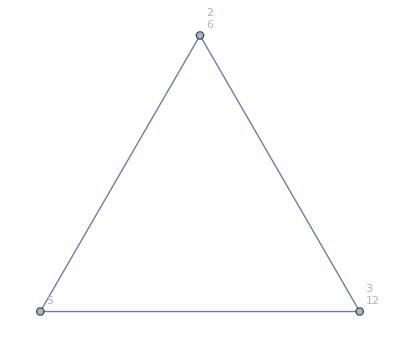
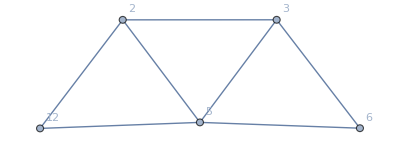
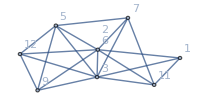
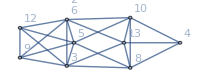
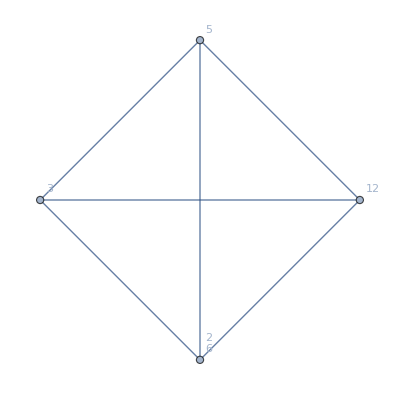
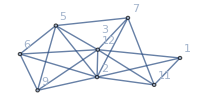
{{10000,9}→-Graphics-303340 | -Graphics-{(-3+x)^4 (-2+x),24,True} | -Graphics-{(-3+x)^2 (-2+x) (-32+29 x-9 x^2+x^3),96,True} | -Graphics-{-2+x,24,True} | -Graphics-
-Graphics-302530 | -Graphics-{(-4+x) (-3+x)^4 (-2+x),0,False} | -Graphics-{(-4+x) (-3+x)^2 (-2+x) (-32+29 x-9 x^2+x^3),0,False} | -Graphics-{(-3+x) (-2+x),24,True} | -Graphics-
-Graphics-296050 | -Graphics-{(-4+x) (-3+x)^4 (-2+x),0,False} | -Graphics-{(-4+x) (-3+x)^2 (-2+x) (-32+29 x-9 x^2+x^3),0,False} | -Graphics-{(-3+x) (-2+x),24,True} | -Graphics-
-Graphics-295250 | -Graphics-{(-4+x) (-3+x)^4 (-2+x),0,False} | -Graphics-{(-4+x) (-3+x)^2 (-2+x) (-32+29 x-9 x^2+x^3),0,False} | -Graphics-{(-3+x) (-2+x),24,True} | -Graphics-
-Graphics-295240 | -Graphics-{(-5+x) (-4+x) (-3+x)^4 (-2+x),0,False} | -Graphics-{(-5+x) (-4+x) (-3+x)^2 (-2+x) (-32+29 x-9 x^2+x^3),0,False} | -Graphics-{(-4+x) (-3+x) (-2+x),0,False} | -Graphics-{2,3,5,12,6},{10000,6}→-Graphics-303340 | -Graphics-{(-3+x)^2 (-2+x)^2,48,True} | -Graphics-{(-3+x)^6 (-2+x),24,True} | -Graphics-{-2+x,24,True} | -Graphics-
-Graphics-302621 | -Graphics-{(-3+x)^3 (-2+x),24,True} | -Graphics-{(-3+x)^6 (-2+x),24,True} | -Graphics-{-2+x,24,True} | -Graphics-
-Graphics-302530 | -Graphics-{(-4+x) (-3+x)^3 (-2+x),0,False} | -Graphics-{(-4+x) (-3+x)^6 (-2+x),0,False} | -Graphics-{(-3+x) (-2+x),24,True} | -Graphics-
-Graphics-296080 | -Graphics-{(-3+x)^3 (-2+x),24,True} | -Graphics-{(-3+x)^6 (-2+x),24,True} | -Graphics-{-2+x,24,True} | -Graphics-
-Graphics-296050 | -Graphics-{(-4+x) (-3+x)^3 (-2+x),0,False} | -Graphics-{(-4+x) (-3+x)^6 (-2+x),0,False} | -Graphics-{(-3+x) (-2+x),24,True} | -Graphics-
-Graphics-295330 | -Graphics-{(-4+x)^2 (-3+x)^2 (-2+x),0,False} | -Graphics-{(-4+x) (-3+x)^6 (-2+x),0,False} | -Graphics-{(-3+x) (-2+x),24,True} | -Graphics-
-Graphics-295270 | -Graphics-{(-4+x)^2 (-3+x)^2 (-2+x),0,False} | -Graphics-{(-4+x) (-3+x)^6 (-2+x),0,False} | -Graphics-{(-3+x) (-2+x),24,True} | -Graphics-
-Graphics-295240 | -Graphics-{(-5+x) (-4+x)^2 (-3+x)^2 (-2+x),0,False} | -Graphics-{(-5+x) (-4+x) (-3+x)^6 (-2+x),0,False} | -Graphics-{(-4+x) (-3+x) (-2+x),0,False} | -Graphics-{3,5,9,13,10},{10000,8}→-Graphics-319540 | -Graphics-{(-3+x) (-2+x),24,True} | -Graphics-{(-3+x)^7 (-2+x),24,True} | -Graphics-{-2+x,24,True} | -Graphics-
-Graphics-317110 | -Graphics-{(-4+x) (-3+x) (-2+x),0,False} | -Graphics-{(-4+x) (-3+x)^7 (-2+x),0,False} | -Graphics-{(-3+x) (-2+x),24,True} | -Graphics-
-Graphics-304961 | -Graphics-{(-3+x) (-2+x),24,True} | -Graphics-{(-3+x)^6 (-2+x)^2,48,True} | -Graphics-{-2+x,24,True} | -Graphics-
-Graphics-303340 | -Graphics-{(-3+x) (-2+x),24,True} | -Graphics-{(-3+x)^7 (-2+x),24,True} | -Graphics-{-2+x,24,True} | -Graphics-
-Graphics-302530 | -Graphics-{(-4+x) (-3+x) (-2+x),0,False} | -Graphics-{(-3+x)^8 (-2+x),24,True} | -Graphics-{(-3+x) (-2+x),24,True} | -Graphics-
-Graphics-297670 | -Graphics-{(-4+x) (-3+x) (-2+x),0,False} | -Graphics-{(-3+x)^8 (-2+x),24,True} | -Graphics-{(-3+x) (-2+x),24,True} | -Graphics-
-Graphics-296050 | -Graphics-{(-4+x) (-3+x) (-2+x),0,False} | -Graphics-{(-4+x) (-3+x)^7 (-2+x),0,False} | -Graphics-{(-3+x) (-2+x),24,True} | -Graphics-
-Graphics-295240 | -Graphics-{(-5+x) (-4+x) (-3+x) (-2+x),0,False} | -Graphics-{(-4+x)^2 (-3+x)^7 (-2+x),0,False} | -Graphics-{(-4+x) (-3+x) (-2+x),0,False} | -Graphics-{3,5,13,4,10},{10000,13}→-Graphics-319540 | -Graphics-{(-3+x) (-2+x),24,True} | -Graphics-{(-3+x)^7 (-2+x),24,True} | -Graphics-{-2+x,24,True} | -Graphics-
-Graphics-317110 | -Graphics-{(-4+x) (-3+x) (-2+x),0,False} | -Graphics-{(-4+x) (-3+x)^7 (-2+x),0,False} | -Graphics-{(-3+x) (-2+x),24,True} | -Graphics-
-Graphics-304961 | -Graphics-{(-3+x) (-2+x),24,True} | -Graphics-{(-3+x)^6 (-2+x)^2,48,True} | -Graphics-{-2+x,24,True} | -Graphics-
-Graphics-303340 | -Graphics-{(-3+x) (-2+x),24,True} | -Graphics-{(-3+x)^7 (-2+x),24,True} | -Graphics-{-2+x,24,True} | -Graphics-
-Graphics-302530 | -Graphics-{(-4+x) (-3+x) (-2+x),0,False} | -Graphics-{(-3+x)^8 (-2+x),24,True} | -Graphics-{(-3+x) (-2+x),24,True} | -Graphics-
-Graphics-297670 | -Graphics-{(-4+x) (-3+x) (-2+x),0,False} | -Graphics-{(-3+x)^8 (-2+x),24,True} | -Graphics-{(-3+x) (-2+x),24,True} | -Graphics-
-Graphics-296050 | -Graphics-{(-4+x) (-3+x) (-2+x),0,False} | -Graphics-{(-4+x) (-3+x)^7 (-2+x),0,False} | -Graphics-{(-3+x) (-2+x),24,True} | -Graphics-
-Graphics-295240 | -Graphics-{(-5+x) (-4+x) (-3+x) (-2+x),0,False} | -Graphics-{(-4+x)^2 (-3+x)^7 (-2+x),0,False} | -Graphics-{(-4+x) (-3+x) (-2+x),0,False} | -Graphics-{3,6,8,4,10},{10000,10}→-Graphics-319540 | -Graphics-{(-3+x) (-2+x),24,True} | -Graphics-{(-3+x)^6 (-2+x)^2,48,True} | -Graphics-{-2+x,24,True} | -Graphics-
-Graphics-317380 | -Graphics-{(-3+x) (-2+x),24,True} | -Graphics-{(-3+x)^7 (-2+x),24,True} | -Graphics-{-2+x,24,True} | -Graphics-
-Graphics-317110 | -Graphics-{(-4+x) (-3+x) (-2+x),0,False} | -Graphics-{(-3+x)^8 (-2+x),24,True} | -Graphics-{(-3+x) (-2+x),24,True} | -Graphics-
-Graphics-304961 | -Graphics-{(-3+x) (-2+x),24,True} | -Graphics-{(-3+x)^7 (-2+x),24,True} | -Graphics-{-2+x,24,True} | -Graphics-
-Graphics-302530 | -Graphics-{(-4+x) (-3+x) (-2+x),0,False} | -Graphics-{(-4+x) (-3+x)^7 (-2+x),0,False} | -Graphics-{(-3+x) (-2+x),24,True} | -Graphics-
-Graphics-297670 | -Graphics-{(-4+x) (-3+x) (-2+x),0,False} | -Graphics-{(-3+x)^8 (-2+x),24,True} | -Graphics-{(-3+x) (-2+x),24,True} | -Graphics-
-Graphics-295510 | -Graphics-{(-4+x) (-3+x) (-2+x),0,False} | -Graphics-{(-4+x) (-3+x)^7 (-2+x),0,False} | -Graphics-{(-3+x) (-2+x),24,True} | -Graphics-
-Graphics-295240 | -Graphics-{(-5+x) (-4+x) (-3+x) (-2+x),0,False} | -Graphics-{(-4+x)^2 (-3+x)^7 (-2+x),0,False} | -Graphics-{(-4+x) (-3+x) (-2+x),0,False} | -Graphics-{5,6,8,13,4}}

```mathematica
With[{k=10000},
Block[{g=ReadGrof[k],vertices, adj},
vertices=Select[VertexList[g],VertexDegree[g,#]==5&];
Table[
adj=AdjacencyList[g,v];
{Style[k,If[OddQ[k],Blue,Purple]],v}->Labeled[Framed[ZykovDecomposition[g,adj]],adj]
,{v,vertices}
]
]
]
```